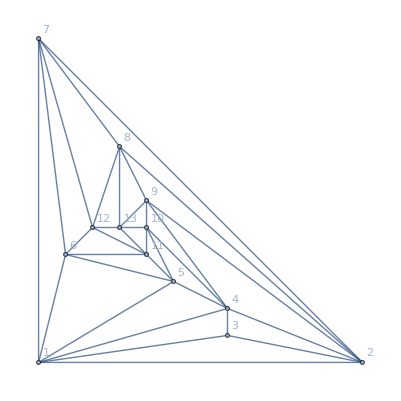

```mathematica
g=Graph[{1,2,3,4,5,6,7,8,9,10,11,12,13},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->7,2<->8,2<->9,2<->4,2<->3,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->12,6<->7,7<->12,7<->8,8<->12,8<->13,8<->9,9<->13,9<->10,10<->13,10<->11,11<->13,11<->12,12<->13},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
MaximalPlanarDirectQ[g]
```

True

```mathematica
Edge
```

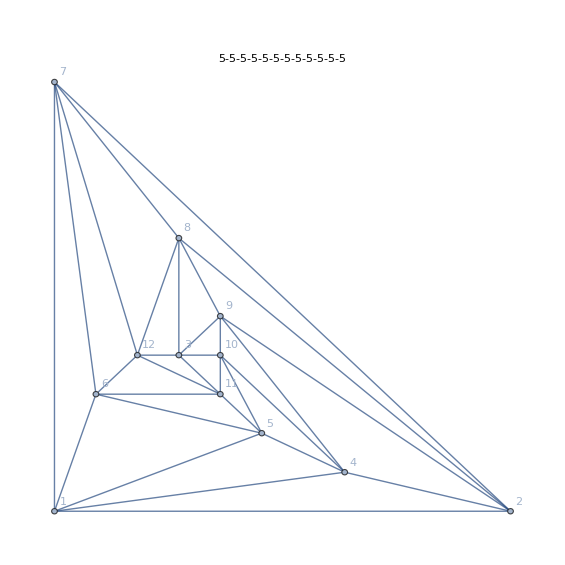

```mathematica
h=Graph[{1,2,3,4,5,6,7,8,9,10,11,12},{1<->2,1<->4,1<->5,1<->6,1<->7,2<->4,2<->7,2<->8,2<->9,3<->8,3<->9,3<->10,3<->11,3<->12,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name",PlotLabel->EdgeCountList[h]]
```

```mathematica
Length[EdgeList[h]]
```

30

```mathematica
Length[VertexList[h]]
```

12

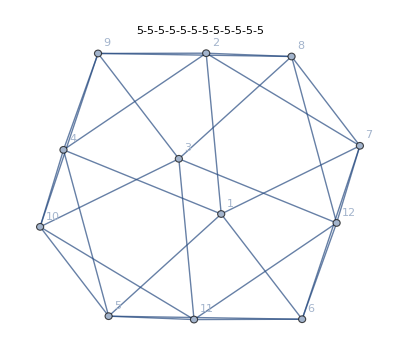

```mathematica
Graph[h, GraphLayout->"SpringElectricalEmbedding"]
```

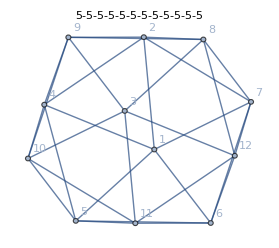
```mathematica
-Graphics-
IsomorphicGraphQ[h, GraphData["IcosahedralGraph"]]
```

-Graphics-

True

True

```mathematica
MaximalPlanarDirectQ[ GraphData["IcosahedralGraph"]]
```

True

```mathematica
EdgeCountList[h]
```

5-5-5-5-5-5-5-5-5-5-5-5

```mathematica
MaximalPlanarDirectQ[h]
```

True

```mathematica
twelve=Monitor[Table[ReadGraph[12,k],{k,1,7594}],k];Length[twelve]
```

7594

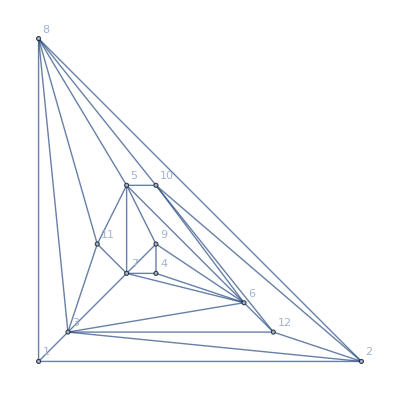

```mathematica
Graph[twelve[[1]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

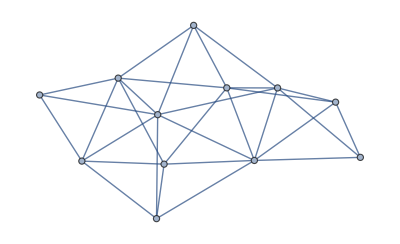

```mathematica
twelve[[1]]
```

```mathematica
EdgeCountList[twelve[[1]]]
```

7-7-6-6-6-5-5-4-4-4-3-3

```mathematica
twelveSmall=Select[twelve,IsomorphicGraphQ[#,h]&];Length[twelveSmall]
```

0

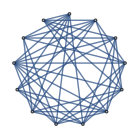

```mathematica
GraphComplement[g]
```

```mathematica
MaximalPlanarDirectQ[ Graph[{1,2,3,4,5,6,7,8,9,10,11,12},{1<->2,1<->4,1<->5,1<->6,1<->7,2<->4,2<->7,2<->8,2<->9,3<->8,3<->9,3<->10,3<->11,3<->12,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]]
```

True

```mathematica
Remove 3

Remove 4
Graph[{1,2,3,5,6,7,8,9,10,11,12,4},{1<->2,1<->3,1<->5,1<->6,1<->7,2<->3,2<->7,2<->8,2<->9,4<->8,4<->9,4<->10,4<->11,4<->12,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 5
Graph[{1,2,3,4,6,7,8,9,10,11,12,5},{1<->2,1<->3,1<->4,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->9,4<->10,5<->8,5<->9,5<->10,5<->11,5<->12,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 6
Graph[{1,2,3,4,5,7,8,9,10,11,12,6},{1<->2,1<->3,1<->4,1<->5,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->5,4<->9,4<->10,5<->10,5<->11,6<->8,6<->9,6<->10,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 7
Graph[{1,2,3,4,5,6,8,9,10,11,12,7},{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->8,2<->9,3<->4,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->11,6<->12,7<->8,7<->9,7<->10,7<->11,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 8
Graph[{1,2,3,4,5,6,7,9,10,11,12,8},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->9,3<->4,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->12,8<->9,8<->10,8<->11,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 9
Graph[{1,2,3,4,5,6,7,8,10,11,12,9},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,3<->4,4<->5,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,9<->11,9<->12,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 10
Graph[{1,2,3,4,5,6,7,8,9,11,12,10},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->5,4<->9,5<->6,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->10,8<->12,9<->10,10<->11,10<->12,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 11
Graph[{1,2,3,4,5,6,7,8,9,10,12,11},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->5,4<->9,4<->10,5<->6,5<->10,6<->7,6<->12,7<->8,7<->12,8<->9,8<->11,8<->12,9<->10,9<->11,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 12
Graph[{1,2,3,4,5,6,7,8,9,10,11,12},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,7<->8,8<->9,8<->12,9<->10,9<->12,10<->11,10<->12,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
Remove 13
Graph[{1,2,3,4,5,6,7,8,9,10,11,12},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->7,2<->8,2<->9,3<->4,4<->5,4<->9,4<->10,5<->6,5<->10,5<->11,6<->7,6<->11,6<->12,7<->8,7<->12,8<->9,8<->12,9<->10,10<->11,11<->12},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

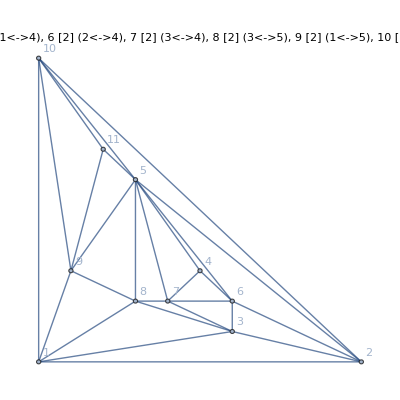

```mathematica
ancestor=Graph[{1,2,3,4,5,6,7,8,9,10,11},{1<->2,1<->3,2<->3,4<->5,2<->5,2<->6,4<->6,3<->6,5<->6,3<->7,4<->7,5<->7,6<->7,3<->8,5<->8,1<->8,7<->8,1<->9,5<->9,8<->9,2<->10,9<->10,1<->10,5<->10,5<->11,9<->11,10<->11},PlotLabel->"0 - K3, 4 [1] (1<->2<->3), 5 [2] (1<->4), 6 [2] (2<->4), 7 [2] (3<->4), 8 [2] (3<->5), 9 [2] (1<->5), 10 [2] (2<->9), 11 [1] (5<->9<->10)",GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
EdgeCountList[ancestor]
```

8-5-5-5-5-5-5-5-5-3-3

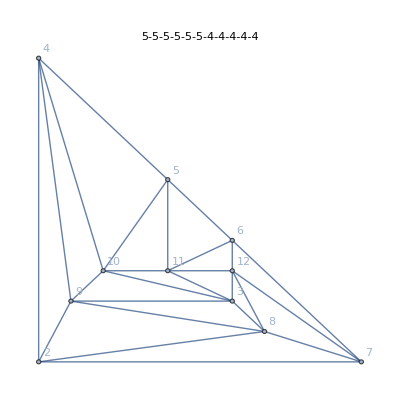
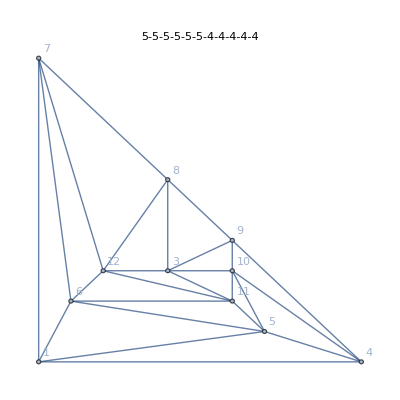
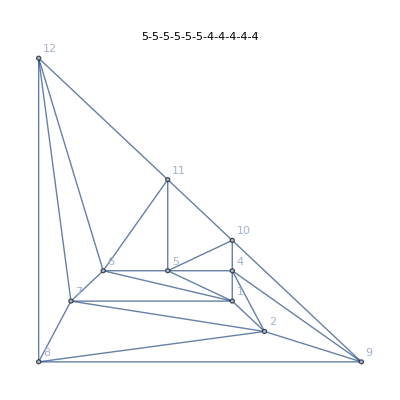
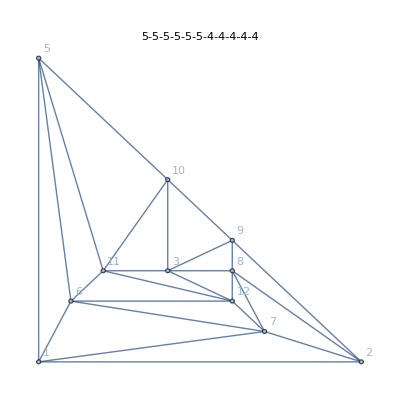
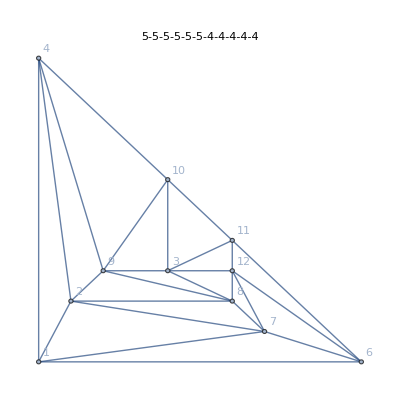
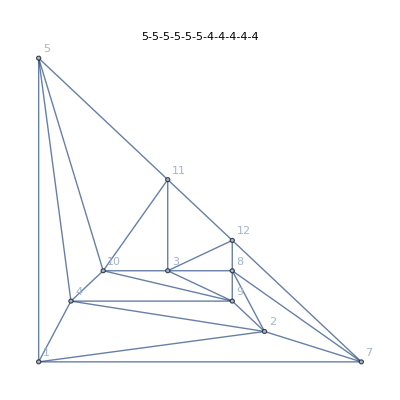
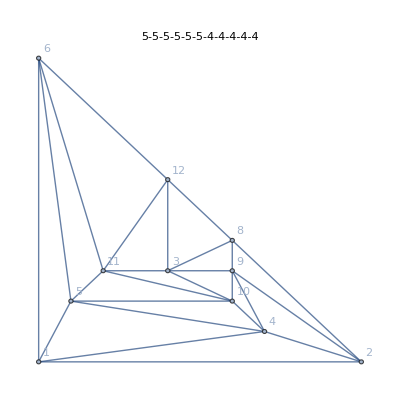
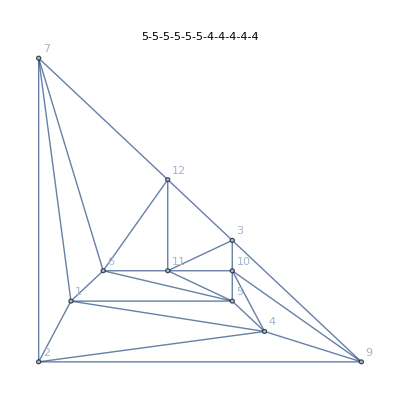
{{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-}}

```mathematica
Table[
With[
{g=VertexDelete[h,v]},
{MaximalPlanarDirectQ[g],Graph[g,PlotLabel->EdgeCountList[g]]}
],{v,VertexList[h]}]
```

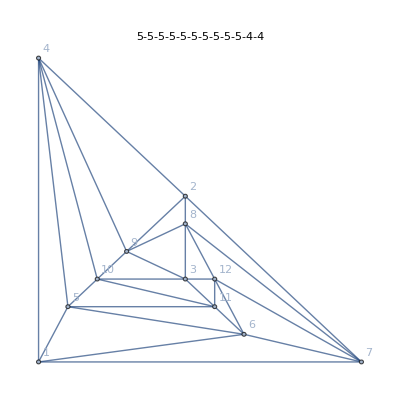
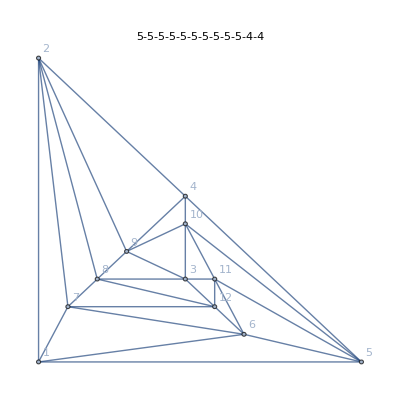
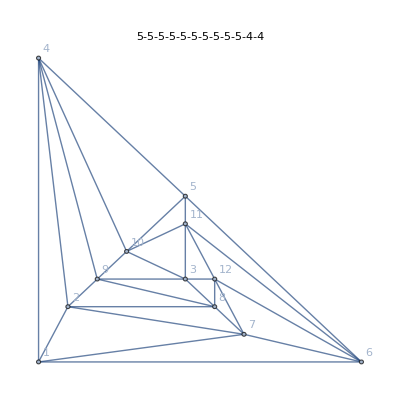
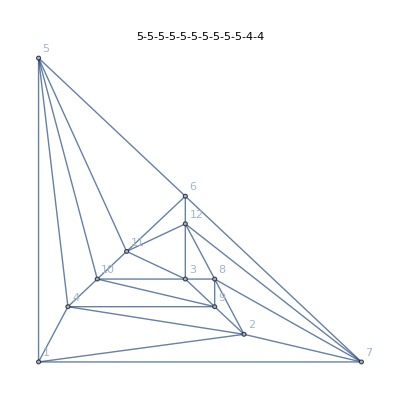
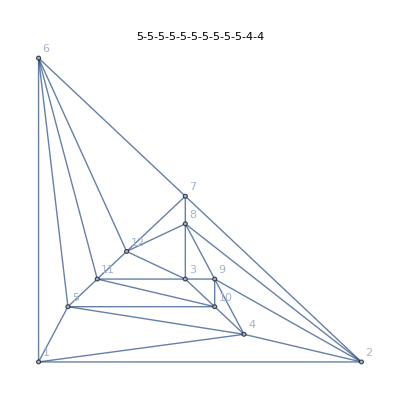
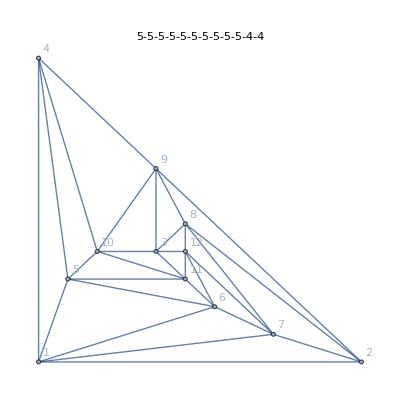
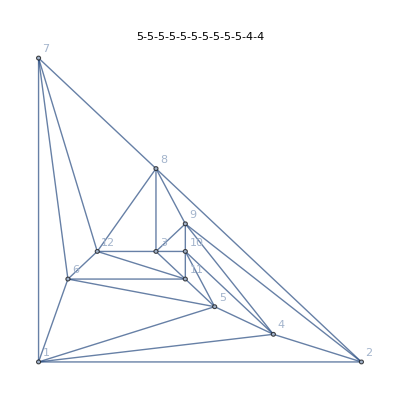
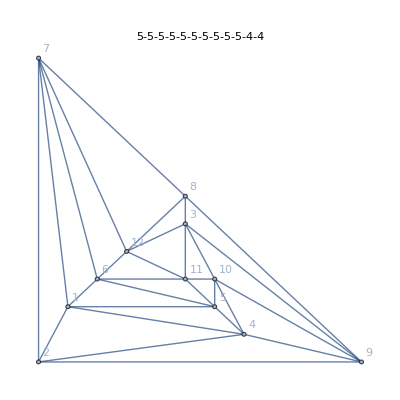
{{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-},{False,-Graphics-}}

```mathematica
Table[
With[
{g=EdgeDelete[h,e]},
{MaximalPlanarDirectQ[g],Graph[g,PlotLabel->EdgeCountList[g]]}
],{e,EdgeList[h]}]
```

```mathematica
eleven=Monitor[Table[ReadGraph[11,k],{k,1,1249}],k];Length[eleven]
```

1249

```mathematica
Map[{Length[EdgeList[GraphDifference[h,#]]],#}&,Select[eleven,Length[EdgeList[GraphDifference[h,#]]]<=8&]]
```

{}

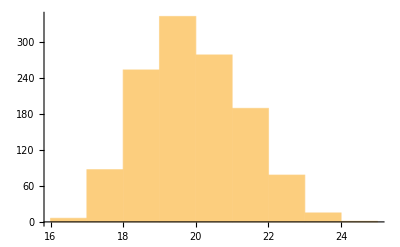

```mathematica
Histogram[Map[Length[EdgeList[GraphDifference[h,#]]]&,eleven]]
```

```mathematica
Length[VertexList[h]]
```

12

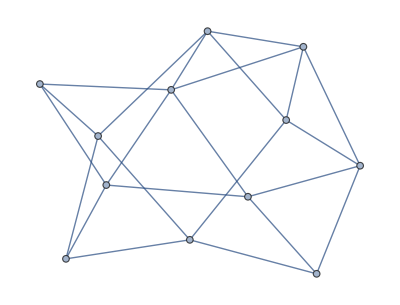
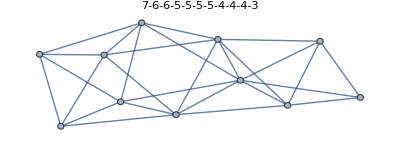
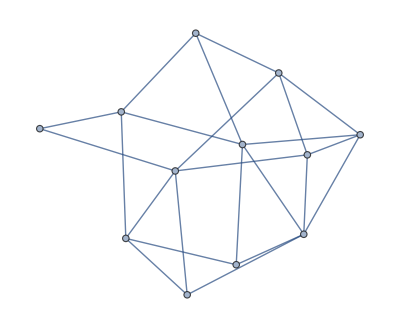
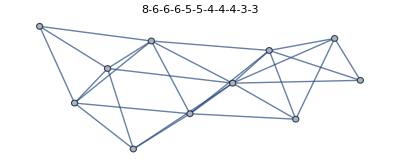
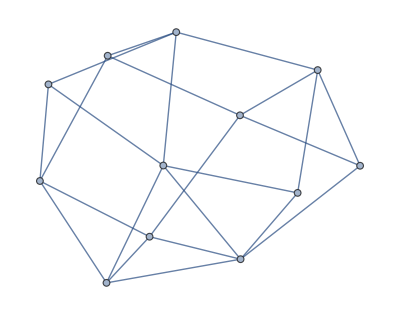
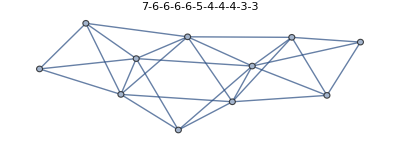
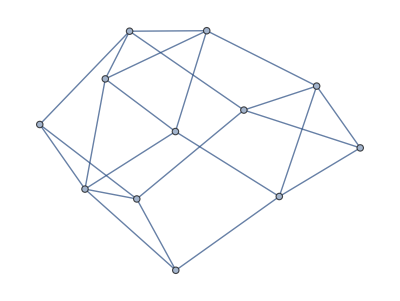
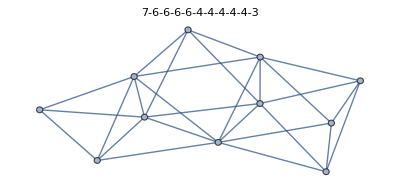
{{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-}}

```mathematica
Map[{Length[EdgeList[GraphIntersection[h,#]]],GraphDifference[h,#],Graph[#, PlotLabel->EdgeCountList[#]]}&,Select[eleven,Length[EdgeList[GraphIntersection[h,#]]]≤7&]]
```

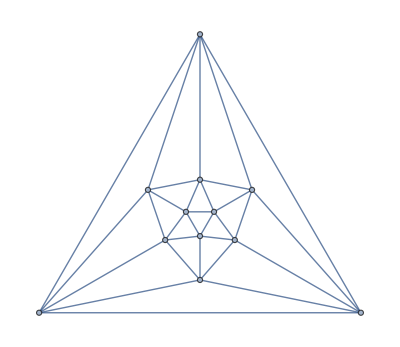

```mathematica
GraphData["IcosahedralGraph"]
```

```mathematica
ChromaticPolynomial[h,4]
```

240

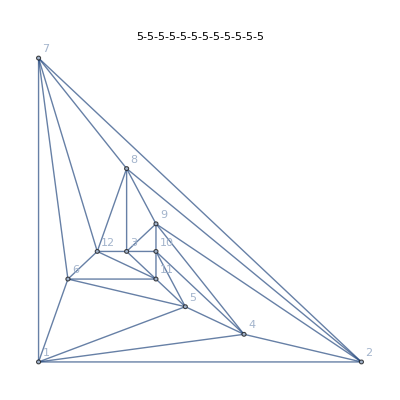

```mathematica
h
```

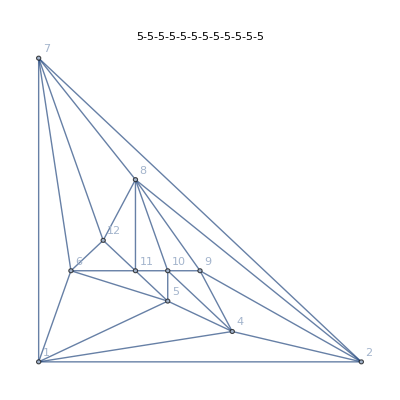

```mathematica
hbis=EdgeAdd[ VertexDelete[h,3],{8<->10,8<->11}]
```

```mathematica
MaximalPlanarDirectQ[hbis]
```

True

```mathematica
Table[{eleven[[k]],k},{k,1,Length[hbis]}]
```

{}

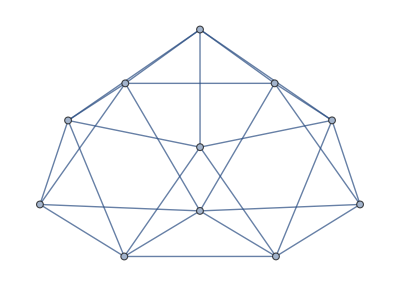
{{-Graphics-,1127}}

```mathematica
Select[Table[{eleven[[k]],k},{k,1,Length[eleven]}],IsomorphicGraphQ[#[[1]],hbis]&]
```

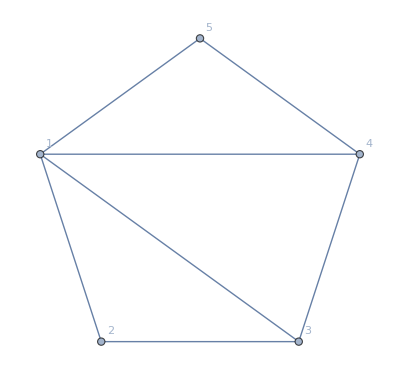

```mathematica
f1=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->3,1<->4}, VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

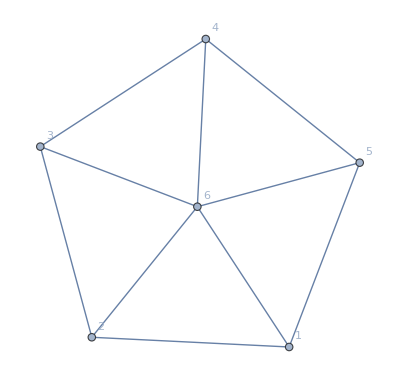

```mathematica
f2=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,3<->6,4<->6,5<->6}, VertexLabels->"Name"]
```

```mathematica
ChromaticPolynomial[f1,4]
```

96

```mathematica
ChromaticPolynomial[f2,4]
```

120

```mathematica
Factor[ChromaticPolynomial[f2,x]/ChromaticPolynomial[f1,x]]
```

((-3+x) (5-4 x+x^2))/(-2+x)^2